## Setting up symmetric and antisymmetric reduced blocks of Hamiltonian describing ZQ spin chain frequencies

```mathematica
HamReducedSymmetric[JAA_,JMM_,JXX_,ΔJAM_,ΔJMX_,ΔJAX_]:=Module[{H},
H = {{1/4 (-3 (JAA+JMM)+JXX),ΔJMX/2,ΔJAX/2,ΔJAM/2},{ΔJMX/2,1/4 (-3 JAA+JMM-3 JXX),ΔJAM/2,ΔJAX/2},{ΔJAX/2,ΔJAM/2,1/4 (JAA-3 (JMM+JXX)),ΔJMX/2},{ΔJAM/2,ΔJAX/2,ΔJMX/2,1/4 (JAA+JMM+JXX)}};
H
]
```

```mathematica
HamReducedAntiSymmetric[JAA_,JMM_,JXX_,ΔJAM_,ΔJMX_,ΔJAX_]:=Module[{H},
H = {{1/4 (-3 JAA+JMM+JXX),ΔJAM/2,ΔJAX/2,ΔJMX/2},{ΔJAM/2,1/4 (JAA-3 JMM+JXX),ΔJMX/2,ΔJAX/2},{ΔJAX/2,ΔJMX/2,1/4 (JAA+JMM-3 JXX),ΔJAM/2},{ΔJMX/2,ΔJAX/2,ΔJAM/2,-3/4 (JAA+JMM+JXX)}};
H
]
```

```mathematica
AbsoluteTiming[Eigensystem[HamReducedSymmetric[-14.0,-14.0,-14.0,-6.06,-6.06,0.0]]]
```

{0.0002407,{{22.0762,17.5,13.5793,-11.1554},{{0.513783,-0.680381,0.513783,-0.0955769},{0.707107,-2.79526×10^-16,-0.707107,0.},{-0.473922,-0.73251,-0.473922,0.119271},{0.106887,0.0226042,0.106887,0.988251}}}}

```mathematica
AbsoluteTiming[Eigenvalues[HamReducedSymmetric[-14.0,-14.0,-14.0,-6.06,-6.06,0.0]]]
```

{0.0085193,{22.0762,17.5,13.5793,-11.1554}}

```mathematica
AbsoluteTiming[Eigenvalues[HamReducedAntiSymmetric[-14.0,-14.0,-14.0,-6.06,-6.06,0.0]]]
```

{0.0000979,{32.1554,7.42072,3.5,-1.07615}}

```mathematica
CalcFreqsIdealized[Jintra_?NumericQ,ΔJ_?NumericQ]:=Module[{i,EigenBasis,SP1,SP2,SP3,N1,N2,N3,En1,En2,En3,f1,f2,f3,freqlist,TM,state1,state2,state3},
TM=HMatrixIdealized[Jintra,ΔJ];

EigenBasis=Eigensystem[TM][[2,All]];

SP1=ConstantArray[0,4];
SP2=ConstantArray[0,4];
SP3=ConstantArray[0,4];

state1=1/2{1,√2,1,0};
state2=1/2{√2,0,-√2,0};
state3=1/2{1,-√2,1,0};


For[i=1,i<=4,i++,
SP1[[i]]=state1.EigenBasis[[i]];
SP2[[i]]=state2.EigenBasis[[i]];
SP3[[i]]=state3.EigenBasis[[i]];
];

N1=Position[Abs[SP1],Max[Abs[SP1]]][[1,1]];
N2=Position[Abs[SP2],Max[Abs[SP2]]][[1,1]];
N3=Position[Abs[SP3],Max[Abs[SP3]]][[1,1]];
En1=Eigensystem[TM][[1,N1]];
En2=Eigensystem[TM][[1,N2]];
En3=Eigensystem[TM][[1,N3]];
f1=Abs[En2-En3];
f2=Abs[En1-En2];
f3=Abs[En1-En3];
freqlist={f1,f2,f3};

freqlist

]
```

```mathematica
NJintra=30;
NΔJ=30;
NdJMM = 10;
NdJXX = 10;

(*NJintra=4;
NΔJ=4;
NdJMM = 4;
NdJXX = 4;*)

JintraMax=-32.0;
JintraMin=-5.0;

ΔJMax=-15.0;
ΔJMin=-0.1;

dJMMMax = 1.0;
dJMMMin = -1.0;

dJXXMax = 1.0;
dJXXMin = -1.0;

dJintra= (JintraMax-JintraMin)/NJintra;
dΔJ = (ΔJMax-ΔJMin)/NΔJ;

ddJMM = (dJMMMax-dJMMMin)/NdJMM;
ddJXX= (dJXXMax-dJXXMin)/NdJXX;
```

```mathematica
Jintra=Range[JintraMin,JintraMax,dJintra];
ΔJ=Range[ΔJMin,ΔJMax,dΔJ];
dJMM = Range[dJMMMin,dJMMMax,ddJMM];
dJXX = Range[dJXXMin,dJXXMax,ddJXX];
```

```mathematica
dJMM
```

{-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.}

```mathematica
ListJs=ConstantArray[0,{(NJintra+1)*(NΔJ+1),2}]; 
Freq1=ConstantArray[0,{(NJintra+1)*(NΔJ+1),3}];
Freq2=ConstantArray[0,{(NJintra+1)*(NΔJ+1),3}];
Freq3=ConstantArray[0,{(NJintra+1)*(NΔJ+1),3}];
```

```mathematica
(NJintra+1)*(NΔJ+1)
```

961

```mathematica
((NJintra+1)*(NΔJ+1))/(60*60)0.099//N(*number of hours per calculation*)
```

0.0264275

```mathematica
((NJintra+1)*(NΔJ+1))/10//N(*number of seconds per calculation*)
```

96.1

```mathematica
AbsoluteTiming[
HMatrixIdealized[x1_ ?NumericQ,x2_ ?NumericQ]:=HamReducedSymmetric[x1,x1,x1,x2,x2,0.0];
CalcFreqsIdealized[-14.0,6.06]]
```

{0.0002348,{3.92072,4.57615,8.49687}}

```mathematica
AbsoluteTiming[
tmp=1;
For[i=1,i<= NJintra+1,i++,
For[j=1,j<=NΔJ+1,j++,

HMatrixIdealized[x1_ ?NumericQ,x2_ ?NumericQ]:=HamReducedSymmetric[x1,x1,x1,x2,x2,0.0];
CalculatedFreqs =CalcFreqsIdealized[Jintra[[i]],ΔJ[[j]]];

ListJs[[tmp,1]]=Jintra[[i]];
ListJs[[tmp,2]]=ΔJ[[j]];

Freq1[[tmp,1]]=Jintra[[i]];
Freq1[[tmp,2]]=ΔJ[[j]];
Freq1[[tmp,3]]=CalculatedFreqs[[1]];

Freq2[[tmp,1]]=Jintra[[i]];
Freq2[[tmp,2]]=ΔJ[[j]];
Freq2[[tmp,3]]=CalculatedFreqs[[2]];

Freq3[[tmp,1]]=Jintra[[i]];
Freq3[[tmp,2]]=ΔJ[[j]];
Freq3[[tmp,3]]=CalculatedFreqs[[3]];

tmp++;
If[Mod[tmp,100]==0,
Print[tmp//N];

];
];
];
Export[NotebookDirectory[]<>"Freq1_sym_v1_ks.tsv",NumberForm[#,{Infinity,6}]&/@Freq1,"Table"];
Export[NotebookDirectory[]<>"Freq2_sym_v1_ks.tsv",NumberForm[#,{Infinity,6}]&/@Freq2,"Table"];
Export[NotebookDirectory[]<>"Freq3_sym_v1_ks.tsv",NumberForm[#,{Infinity,6}]&/@Freq3,"Table"];
]
```

100.

200.

300.

400.

500.

600.

700.

800.

900.

{0.567863,Null}

```mathematica
ListPlot3D[{Freq1,Freq2}]
```

-Graphics3D-

```mathematica
ListPlot3D[Freq2]
```

-Graphics3D-

```mathematica
ListPlot3D[Freq3]
```

-Graphics3D-

## Calculating non idealized case with Jintra different

```mathematica
CalcFreqsJintraDifferent[Jintra_?NumericQ,ΔJ_?NumericQ,ΔJMM_?NumericQ,ΔJXX_?NumericQ]:=Module[{i,SP,EigenBasis,SP1,SP2,SP3,N1,N2,N3,En1,En2,En3,f1,f2,f3,freqlist,TM,state1,state2,state3},

TM=HMatrixJintraDifferent[Jintra,ΔJ,ΔJMM,ΔJXX];

EigenBasis=Eigensystem[TM][[2,All]];

SP1=ConstantArray[0,4];
SP2=ConstantArray[0,4];
SP3=ConstantArray[0,4];

state1=1/2{1,√2,1,0};
state2=1/2{√2,0,-√2,0};
state3=1/2{1,-√2,1,0};


For[i=1,i<=4,i++,
SP1[[i]]=state1.EigenBasis[[i]];
SP2[[i]]=state2.EigenBasis[[i]];
SP3[[i]]=state3.EigenBasis[[i]];
];

N1=Position[Abs[SP1],Max[Abs[SP1]]][[1,1]];
N2=Position[Abs[SP2],Max[Abs[SP2]]][[1,1]];
N3=Position[Abs[SP3],Max[Abs[SP3]]][[1,1]];
En1=Eigensystem[TM][[1,N1]];
En2=Eigensystem[TM][[1,N2]];
En3=Eigensystem[TM][[1,N3]];
f1=Abs[En2-En3];
f2=Abs[En1-En2];
f3=Abs[En1-En3];
freqlist={f1,f2,f3};

freqlist

]
```

```mathematica
NJintra=20;
NΔJ=10;
NdJMM = 5;
NdJXX = 3;

(*NJintra=4;
NΔJ=4;
NdJMM = 4;
NdJXX = 4;*)

JintraMax=-32.0;
JintraMin=-5.0;

ΔJMax=-15.0;
ΔJMin=-3.0;

dJMMMax = 1.0;
dJMMMin = -1.0;

dJXXMax = 1.0;
dJXXMin = -1.0;

dJintra= (JintraMax-JintraMin)/NJintra;
dΔJ = (ΔJMax-ΔJMin)/NΔJ;

ddJMM = (dJMMMax-dJMMMin)/NdJMM;
ddJXX= (dJXXMax-dJXXMin)/NdJXX;
```

```mathematica
Jintra=Range[JintraMin,JintraMax,dJintra];
ΔJ=Range[ΔJMin,ΔJMax,dΔJ];
dJMM = Range[dJMMMin,dJMMMax,ddJMM];
dJXX = Range[dJXXMin,dJXXMax,ddJXX];
```

```mathematica
dJMM
```

{-1.,-0.6,-0.2,0.2,0.6,1.}

```mathematica
dJXX
```

{-1.,-0.333333,0.333333,1.}

```mathematica
ListJs=ConstantArray[0,{(NJintra+1)*(NΔJ+1)*(NdJMM+1)*(NdJXX+1),4}]; 
Freq1=ConstantArray[0,{(NJintra+1)*(NΔJ+1)*(NdJMM+1)*(NdJXX+1),5}];
Freq2=ConstantArray[0,{(NJintra+1)*(NΔJ+1)*(NdJMM+1)*(NdJXX+1),5}];
Freq3=ConstantArray[0,{(NJintra+1)*(NΔJ+1)*(NdJMM+1)*(NdJXX+1),5}];
```

```mathematica
(NJintra+1)*(NΔJ+1)*(NdJMM+1)*(NdJXX+1)
```

5544

```mathematica
((NJintra+1)*(NΔJ+1)*(NdJMM+1)*(NdJXX+1))/(60*60)0.001//N(*number of hours per calculation*)
```

0.00231

```mathematica
(NJintra+1)*(NΔJ+1)*(NdJMM+1)*(NdJXX+1)0.001//N(*number of seconds per calculation*)
```

8.316

```mathematica
AbsoluteTiming[
HMatrixJintraDifferent[x1_,x2_,x3_,x4_]:=HamReducedSymmetric[x1,x1+x3,x1+x4,x2,x2,0.0];
CalcFreqsJintraDifferent[-14.0,6.06,0.0,0.0]
]
```

{0.0511848,{3.92072,4.57615,8.49687}}

```mathematica
AbsoluteTiming[
tmp=1;
For[i=1,i<= NJintra+1,i++,
For[j=1,j<=NΔJ+1,j++,
For[k=1,k<=NdJMM+1,k++,
For[l=1,l<=NdJXX+1,l++,

HMatrixJintraDifferent[x1_ ?NumericQ,x2_ ?NumericQ,x3_ ?NumericQ,x4_ ?NumericQ]:=HamReducedSymmetric[x1,x1+x3,x1+x4,x2,x2,0.0];
CalculatedFreqs =CalcFreqsJintraDifferent[Jintra[[i]],ΔJ[[j]],dJMM[[k]],dJXX[[l]]];



Freq1[[tmp,1]]=Jintra[[i]];
Freq1[[tmp,2]]=ΔJ[[j]];
Freq1[[tmp,3]]=dJMM[[k]];
Freq1[[tmp,4]]=dJXX[[l]];
Freq1[[tmp,5]]=CalculatedFreqs[[1]];

Freq2[[tmp,1]]=Jintra[[i]];
Freq2[[tmp,2]]=ΔJ[[j]];
Freq2[[tmp,3]]=dJMM[[k]];
Freq2[[tmp,4]]=dJXX[[l]];
Freq2[[tmp,5]]=CalculatedFreqs[[2]];

Freq3[[tmp,1]]=Jintra[[i]];
Freq3[[tmp,2]]=ΔJ[[j]];
Freq3[[tmp,3]]=dJMM[[k]];
Freq3[[tmp,4]]=dJXX[[l]];
Freq3[[tmp,5]]=CalculatedFreqs[[3]];

tmp++;
If[Mod[tmp,1000]==0,
Print[tmp//N];
];
];
];
];
];
Export[NotebookDirectory[]<>"Freq1_sym_JintraDifferent_v0_ks.tsv",NumberForm[#,{Infinity,6}]&/@Freq1,"Table"];
Export[NotebookDirectory[]<>"Freq2_sym_JintraDifferent_v0_ks.tsv",NumberForm[#,{Infinity,6}]&/@Freq2,"Table"];
Export[NotebookDirectory[]<>"Freq3_sym_JintraDifferent_v0_ks.tsv",NumberForm[#,{Infinity,6}]&/@Freq3,"Table"];
]
```

1000.

2000.

3000.

4000.

5000.

{3.1791,Null}

### Plotting resulted surfaces

```mathematica
ClearAll[PlotFixedCoordinates]

PlotFixedCoordinates[dataFile_String,fixedCoords_List,plotType_:"3D"]:=Module[{data,coords,values,combinedData,nCoords,fixedIndices,variableIndices,filtered,plotData,labels,sortedVars,xVals,yVals,gridCheck,zGrid,plot,xIndex,yIndex,axisNames,plotTypeLocal,rawLines},(*Normalize plot type safely*)plotTypeLocal=ToUpperCase@ToString[plotType];
If[!MemberQ[{"2D","3D"},plotTypeLocal],Return["❌ Plot type must be either '2D' or '3D'."]];
(*Load and parse data*)rawLines=Import[dataFile,"Lines"];
data=Select[ToExpression/@rawLines,VectorQ[#,NumericQ]&];
If[Length[data]<2||Length[data[[1]]]<2,Return["❌ Invalid or insufficient data loaded from file."]];
(*Separate coordinates and function values*)coords=Most/@data;
values=Last/@data;
combinedData=MapThread[Append,{coords,values}];
(*Determine fixed vs variable coordinates*)fixedAssoc=If[Head[fixedCoords]===Association,fixedCoords,Association[fixedCoords]];
nCoords=Length[coords[[1]]];
fixedIndices=Keys[fixedAssoc];
variableIndices=Complement[Range[nCoords],fixedIndices];
If[Length[variableIndices]<1||Length[variableIndices]>2,Return["❌ You must vary exactly 1 or 2 coordinates to generate a plot."]];
(*Filter data near fixed coordinates*)filtered=Select[combinedData,Function[row,And@@Table[Abs[row[[i]]-fixedAssoc[i]]<0.001,{i,fixedIndices}]]];
If[Length[filtered]<2,Print["⚠️ No matches found for: ",fixedAssoc];
Do[Print["Available values for coord ",i,": ",Take[Union[combinedData[[All,i]]],UpTo[10]],"..."],{i,Range[nCoords]}];
Return["❌ No matching data found for given fixed coordinates."]];
(*Prepare axis names and sorted variable indices*)axisNames=<|1->"Jintra",2->"deltaJ",3->"dJMM",4->"dJXX"|>;
sortedVars=Sort[variableIndices];
plotData=filtered[[All,Join[sortedVars,{nCoords+1}]]];
(*3D surface plot*)If[plotTypeLocal=="3D"&&Length[sortedVars]==2,{xIndex,yIndex}=sortedVars;
xVals=Union[plotData[[All,1]]];
yVals=Union[plotData[[All,2]]];
labels={axisNames[xIndex],axisNames[yIndex],"f(x)"};
gridCheck=Length[xVals]*Length[yVals]==Length[plotData];
If[gridCheck,(*Structured grid surface*)zGrid=Table[Module[{match},match=Select[plotData,Abs[#[[1]]-xVals[[i]]]<0.0001&&Abs[#[[2]]-yVals[[j]]]<0.0001&];
If[Length[match]>0,match[[1,3]],Missing["NA"]]],{j,Length[yVals]},{i,Length[xVals]}];
plot=ListPlot3D[zGrid,DataRange->{{Min[xVals],Max[xVals]},{Min[yVals],Max[yVals]}},AxesLabel->labels,ColorFunction->"Rainbow",Mesh->All,PlotRange->All];,(*Fallback for non-grid data*)plot=Graphics3D[{Opacity[0.6],PointSize[Small],Point/@plotData[[All,{1,2,3}]],Tube[plotData[[All,{1,2,3}]],0.01]},Axes->True,AxesLabel->labels];];
Return[plot];];
(*2D projection line plot*)If[plotTypeLocal=="2D"&&Length[sortedVars]==1,labels={axisNames[sortedVars[[1]]],"f(x)"};
Return[ListLinePlot[SortBy[plotData,First],AxesLabel->labels,PlotRange->All]];];
Return["❌ Unsupported plot configuration."]]
```

```mathematica
G[1]=PlotFixedCoordinates[NotebookDirectory[]<>"Freq1_sym_JintraDifferent_v0_ks.tsv",{1->-13.1,2->-6.6},"3D"]
G[2]=PlotFixedCoordinates[NotebookDirectory[]<>"Freq2_sym_JintraDifferent_v0_ks.tsv",{1->-13.1,2->-6.6},"3D"]
Show[G[1],G[2]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Jintra
```

{-5.,-6.35,-7.7,-9.05,-10.4,-11.75,-13.1,-14.45,-15.8,-17.15,-18.5,-19.85,-21.2,-22.55,-23.9,-25.25,-26.6,-27.95,-29.3,-30.65,-32.}

```mathematica
ΔJ
```

{-3.,-4.2,-5.4,-6.6,-7.8,-9.,-10.2,-11.4,-12.6,-13.8,-15.}

```mathematica
dJMM
```

{-1.,-0.6,-0.2,0.2,0.6,1.}

```mathematica
dJXX
```

{-1.,-0.333333,0.333333,1.}

```mathematica
PlotFixedCoordinates[NotebookDirectory[]<>"Freq1_sym_JintraDifferent_v0_ks.tsv",{3->0.2,4->0.33333},"3D"]
```

-Graphics3D-

```mathematica
dJMM
```

{-1.,-0.6,-0.2,0.2,0.6,1.}

```mathematica
PlotFixedCoordinates[NotebookDirectory[]<>"Freq1_sym_JintraDifferent_v0_ks.tsv",{1->-13.1, 3->0.2},"3D"]
```

-Graphics3D-

```mathematica
PlotFixedCoordinates[NotebookDirectory[]<>"Freq2_sym_JintraDifferent_v0_ks.tsv",{1->-13.1, 4->0.2},"3D"]
```

-Graphics3D-

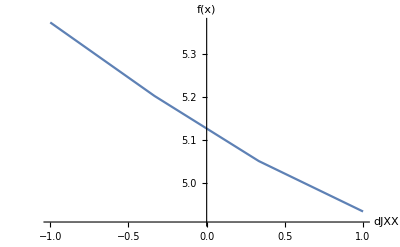

```mathematica
PlotFixedCoordinates[NotebookDirectory[]<>"Freq1_sym_JintraDifferent_v0_ks.tsv",{1->-13.1, 3->0.2,2->-6.6},"2D"]
```

```mathematica
G[1]=PlotFixedCoordinates[NotebookDirectory[]<>"Freq1_sym_JintraDifferent_v0_ks.tsv",{1->-5.0,2->-6.6},"3D"]
G[2]=PlotFixedCoordinates[NotebookDirectory[]<>"Freq2_sym_JintraDifferent_v0_ks.tsv",{1->-5.0,2->-6.6},"3D"]
Show[G[1],G[2]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-